## Attempts at Getting Chern Number

```mathematica
Manipulate[
ParametricPlot3D[{{Sin[px],Sin[py],2-m-c*Cos[px]-d*Cos[py]},{px,py,0}},{px,-π,π},{py,-π,0},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-4,4}}
],
{m,-5,5},{c,0,2},{d,0,2}
]
```

```mathematica
ParametricPlot3D[{{Sin[px],Sin[py],2-1-Cos[px]-Cos[py]}},{px,-π,π},{py,-π,π},
PlotLabel->"m="<>ToString[1],Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
pic1=Table[
ParametricPlot3D[{{Sin[px],Sin[py],2-m-Cos[px]-Cos[py]},{px,py,0}},{px,-π,π},{py,-π,π},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-4,4}},PlotLabel->"m="<>ToString[m]
],
{m,-1,5,1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListPointPlot3D[
ParallelTable[ {Sin[px],Sin[py],2-1-Cos[px]-Cos[py]},{px,-π,π,0.05},{py,-π,π,0.05}],AxesLabel->{x,y,z}
]
```

-Graphics3D-

The following is wrong.

```mathematica
f11[x_,y_,m_]:=2-m+√(1-x^2)+√(1-y^2);
f12[x_,y_,m_]:=2-m+√(1-x^2)-√(1-y^2);
f21[x_,y_,m_]:=2-m-√(1-x^2)+√(1-y^2);
f22[x_,y_,m_]:=2-m-√(1-x^2)-√(1-y^2);
f11x[x_,y_,m_]:={1,0,D[f11[x,y,m],x]};
f11y[x_,y_,m_]:={0,1,D[f11[x,y,m],y]};
numerator11[x_,y_,m_]:=Cross[f11x[x,y,m],f11y[x,y,m]].{x,y,f11[x,y,m]}
denominator11[x_,y_,m_]:=(x^2+y^2+f11[x,y,m]^2)^(3/2);

f12x[x_,y_,m_]:={1,0,D[f12[x,y,m],x]};
f12y[x_,y_,m_]:={0,1,D[f12[x,y,m],y]};
numerator12[x_,y_,m_]:=Cross[f12x[x,y,m],f12y[x,y,m]].{x,y,f12[x,y,m]}
denominator12[x_,y_,m_]:=(x^2+y^2+f12[x,y,m]^2)^(3/2);

f21x[x_,y_,m_]:={1,0,D[f21[x,y,m],x]};
f21y[x_,y_,m_]:={0,1,D[f21[x,y,m],y]};
numerator21[x_,y_,m_]:=Cross[f21x[x,y,m],f21y[x,y,m]].{x,y,f21[x,y,m]}
denominator21[x_,y_,m_]:=(x^2+y^2+f21[x,y,m]^2)^(3/2);

f22x[x_,y_,m_]:={1,0,D[f22[x,y,m],x]};
f22y[x_,y_,m_]:={0,1,D[f22[x,y,m],y]};
numerator22[x_,y_,m_]:=Cross[f22x[x,y,m],f22y[x,y,m]].{x,y,f22[x,y,m]}
denominator22[x_,y_,m_]:=(x^2+y^2+f22[x,y,m]^2)^(3/2);
ChernNumber[m_]:=(NIntegrate[numerator11[x,y,m]/denominator11[x,y,m],{x,-1,1},{y,-1,1}]+NIntegrate[numerator12[x,y,m]/denominator12[x,y,m],{x,-1,1},{y,-1,1}]+NIntegrate[numerator21[x,y,m]/denominator21[x,y,m],{x,-1,1},{y,-1,1}]+NIntegrate[numerator22[x,y,m]/denominator22[x,y,m],{x,-1,1},{y,-1,1}])/(4π);
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

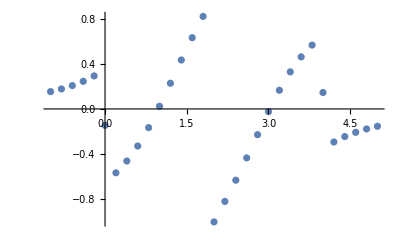

```mathematica
ListPlot[
ParallelTable[{m,ChernNumber[m]},{m,-1,5,0.2}]
]
```

```mathematica
Manipulate[
{Plot3D[{f11[x,y,m],f12[x,y,m],f21[x,y,m],f22[x,y,m]},{x,-1,1},{y,-1,1},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-2.5,2.5}},BoxRatios->{3, 3, 5},PlotStyle->{Red, Blue,Green,Yellow}
],
Plot3D[{f11[x,y,m],f22[x,y,m]},{x,-1,1},{y,-1,1},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-2.5,2.5}},BoxRatios->{3, 3, 5},PlotStyle->{Red,Yellow}
],
Plot3D[{f12[x,y,m],f21[x,y,m]},{x,-1,1},{y,-1,1},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-2.5,2.5}},BoxRatios->{3, 3, 5},PlotStyle->{Blue,Green}
]
},
{m,2,5}
]
```

```mathematica
normalization[px_,py_,m_]:=Norm[{Sin[px],Sin[py],2-m-Cos[px]-Cos[py]}];
```

```mathematica
Manipulate[
ParametricPlot3D[{{Sin[px]/normalization[px,py,m],Sin[py]/normalization[px,py,m],(2-m-Cos[px]-Cos[py])/normalization[px,py,m]},{px,py,0}},{px,-π,π},{py,-π,π},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-5,5}}
],
{m,-5,5}
]
```

```mathematica
normalizedf11[x_,y_,m_]:={x,y,f11[x,y,m]}/Sqrt[x^2+y^2+f11[x,y,m]^2];
normalizedf12[x_,y_,m_]:={x,y,f12[x,y,m]}/Sqrt[x^2+y^2+f12[x,y,m]^2];
normalizedf21[x_,y_,m_]:={x,y,f21[x,y,m]}/Sqrt[x^2+y^2+f21[x,y,m]^2];
normalizedf22[x_,y_,m_]:={x,y,f22[x,y,m]}/Sqrt[x^2+y^2+f22[x,y,m]^2];
```

```mathematica
Manipulate[
ParametricPlot3D[{normalizedf11[x,y,m],normalizedf12[x,y,m],normalizedf21[x,y,m],normalizedf22[x,y,m]},{x,-1,1},{y,-1,1},
AxesLabel->{x,y,z}
],
{m,-5,5}
]
```

```mathematica
patches=GraphicsGrid[{{ParametricPlot3D[normalizedf11[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->{x,y,z}],ParametricPlot3D[normalizedf12[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->{x,y,z}],ParametricPlot3D[normalizedf21[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->{x,y,z}],ParametricPlot3D[normalizedf22[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->{x,y,z}]}},
ImageSize->Large
]
```

-Graphics-

```mathematica
rxnormalizedf11[x_,y_,m_]:={D[normalizedf11[x,y,m][[1]],x],D[normalizedf11[x,y,m][[2]],x],D[normalizedf11[x,y,m][[3]],x]};
rynormalizedf11[x_,y_,m_]:={D[normalizedf11[x,y,m][[1]],y],D[normalizedf11[x,y,m][[2]],y],D[normalizedf11[x,y,m][[3]],y]};
rxnormalizedf12[x_,y_,m_]:={D[normalizedf12[x,y,m][[1]],x],D[normalizedf12[x,y,m][[2]],x],D[normalizedf12[x,y,m][[3]],x]};
rynormalizedf12[x_,y_,m_]:={D[normalizedf12[x,y,m][[1]],y],D[normalizedf12[x,y,m][[2]],y],D[normalizedf12[x,y,m][[3]],y]};
rxnormalizedf21[x_,y_,m_]:={D[normalizedf21[x,y,m][[1]],x],D[normalizedf21[x,y,m][[2]],x],D[normalizedf21[x,y,m][[3]],x]};
rynormalizedf21[x_,y_,m_]:={D[normalizedf21[x,y,m][[1]],y],D[normalizedf21[x,y,m][[2]],y],D[normalizedf21[x,y,m][[3]],y]};
rxnormalizedf22[x_,y_,m_]:={D[normalizedf22[x,y,m][[1]],x],D[normalizedf22[x,y,m][[2]],x],D[normalizedf22[x,y,m][[3]],x]};
rynormalizedf22[x_,y_,m_]:={D[normalizedf22[x,y,m][[1]],y],D[normalizedf22[x,y,m][[2]],y],D[normalizedf22[x,y,m][[3]],y]};
```

The following is wrong.

```mathematica
ChernNumber2[m_]:=
(
NIntegrate[Norm[Cross[rxnormalizedf11[x,y,1],rynormalizedf11[x,y,1]]],{x,-1,1},{y,-1,1}]+
NIntegrate[Norm[Cross[rxnormalizedf12[x,y,1],rynormalizedf12[x,y,1]]],{x,-1,1},{y,-1,1}]+
NIntegrate[Norm[Cross[rxnormalizedf21[x,y,1],rynormalizedf21[x,y,1]]],{x,-1,1},{y,-1,1}]+
NIntegrate[Norm[Cross[rxnormalizedf22[x,y,1],rynormalizedf22[x,y,1]]],{x,-1,1},{y,-1,1}]
)/(4*π);
```